```mathematica
MatrixForm[Partition[Permute[Range[9],RandomPermutation[9]],3]]
```

```mathematica
mat=({{3, 8, 2}, {7, 5, 9}, {1, 6, 4}});
```

```mathematica
pts[m_]:=Table[First[Position[m,i]],{i,1,Length[m]^2}]
```

```mathematica
pts[mat]
```

{{3,1},{1,3},{1,1},{3,3},{2,2},{3,2},{2,1},{1,2},{2,3}}

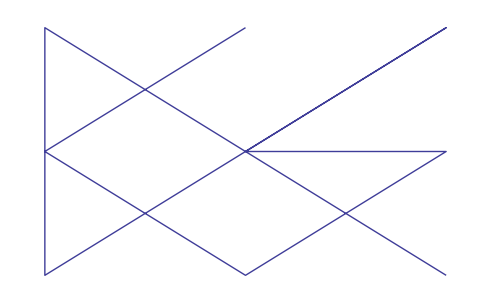

```mathematica
ListPlot[%,Joined->True,Axes->False]
```

```mathematica
lines[l_]:=Table[{l[[i]],l[[i+1]]},{i,1,Length[l]-1}]
```

```mathematica
lines[Flatten[mat]]
```

{{3,8},{8,2},{2,7},{7,5},{5,9},{9,1},{1,6},{6,4}}

```mathematica
lines[pts[mat]]
```

```mathematica
ll={{{3,1},{1,3}},{{1,3},{1,1}},{{1,1},{3,3}},{{3,3},{2,2}},{{2,2},{3,2}},{{3,2},{2,1}},{{2,1},{1,2}},{{1,2},{2,3}}};
```

```mathematica
{{1,2},{3,4}}[[2,2]]
```

4

```mathematica
1==1||1==2
```

True

```mathematica
Select[ll,#[[1,1]]≠#[[2,1]]&]
```

```mathematica
ll={{{3,1},{1,3}},{{1,1},{3,3}},{{3,3},{2,2}},{{2,2},{3,2}},{{3,2},{2,1}},{{2,1},{1,2}},{{1,2},{2,3}}}
```

```mathematica
Length[{{{3,1},{1,3}},{{1,1},{3,3}},{{3,3},{2,2}},{{2,2},{3,2}},{{3,2},{2,1}},{{2,1},{1,2}},{{1,2},{2,3}}}]
```

7

```mathematica
ss=x->3
```

x→3

```mathematica
{x,2x}/.ss
```

{3,6}

```mathematica
Solve[{1a+b==3,3 a+b==1}]
```

{{a→-1,b→4}}

```mathematica
Solve[{4a+b==0,1a+b==4}]
```

{{a→-4/3,b→16/3}}

```mathematica
-4/3 x+16/3==
```

```mathematica
{x,InterpolatingPolynomial[{{3,1},{1,3}},x]}/.Solve[InterpolatingPolynomial[{{3,1},{1,3}},x]==InterpolatingPolynomial[{{4,0},{1,4}},x],x]
```

{{4,0}}

```mathematica
Table[Table[Piecewise[{{{}, i==j}, {Block[{s=Solve[InterpolatingPolynomial[ll[[i]],x]==InterpolatingPolynomial[ll[[j]],x],x]},({x,InterpolatingPolynomial[ll[[i]],x]}/.s)], i≠j}}],{i,1,j}],{j,1,7}]
```

{{{}},{{{2,2}},{}},{{{2,2}},{{x,x}},{}},{{{2,2}},{{2,2}},{{2,2}},{}},{{{5/2,3/2}},{x,x},{x,x},{{3,2}},{}},{{x,4-x},{{3/2,3/2}},{{3/2,3/2}},{{1,2}},{{2,1}},{}},{{{3/2,5/2}},{x,x},{x,x},{{1,2}},{x,-1+x},{{1,2}},{}}}

```mathematica
Piecewise[{{□, □}, {□, □}}]
```

{{{}},{{{2,2}},{}},{{{2,2}},{{x,x}},{}},{{{2,2}},{{2,2}},{{2,2}},{}},{{{5/2,3/2}},{x,x},{x,x},{{3,2}},{}},{{x,4-x},{{3/2,3/2}},{{3/2,3/2}},{{1,2}},{{2,1}},{}},{{{3/2,5/2}},{x,x},{x,x},{{1,2}},{x,-1+x},{{1,2}},{}}}

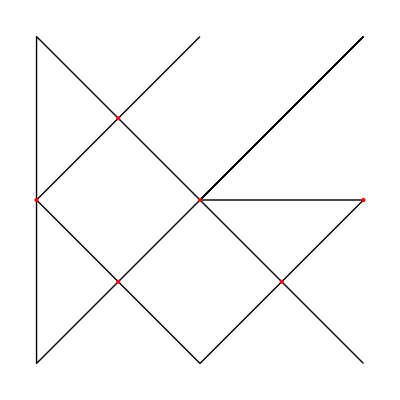

```mathematica
Graphics[{{Line[{{3,1},{1,3},{1,1},{3,3},{2,2},{3,2},{2,1},{1,2},{2,3}}]},{PointSize[Large],Red,Point[{{2,2},{5/2,3/2},{3,2},{1,2},{3/2,5/2},{3/2,3/2}}]}}]
```

```mathematica
Table[Piecewise[{{0, i==j}, {{i,j}, □}}]
```

```mathematica
TopHatTransform[ColorNegate[Binarize[ListLinePlot[{{3,1},{1,3},{1,1},{3,3},{2,2},{3,2},{2,1},{1,2},{2,3}},Joined->True,Axes->False,PlotStyle->Thick]]],2]
```

-Graphics-

```mathematica
Thinning[Binarize[ColorNegate[Graphics[{Thin,Line[{{3,1},{1,3},{1,1},{3,3},{2,2},{3,2},{2,1},{1,2},{2,3},{2,2}}]}]]],10]
```

-Graphics-

```mathematica
MorphologicalGraph[%,EdgeWeight->Automatic]
```

-Graphics-

```mathematica
AdjacencyGraph[AdjacencyMatrix[%]]
```

-Graphics-

```mathematica
Plot[{Sin[x],Cos[x]},{x,-5,5}]
```

```mathematica
6155/60//N
```

102.583

```mathematica
Monitor[Table[Length[FactorInteger[2^n-1]],{n,50,30000,50}],Print[n]]
```

$Aborted

```mathematica
Do[Print[j];Do[FactorInteger[76887698765+i],{i,100}],{j,10}]
```

1

2

3

4

5

6

7

8

9

10

```mathematica
17000/(60*60)//N
```

4.72222

```mathematica
186304/64
```

2911

```mathematica
850/3/60
```

```mathematica
85/18//N
```

4.72222

```mathematica
Monitor[Table[Abs[Det[Partition[Permute[Range[16],RandomPermutation[16]],4]]],{i,1,10000000}],i]
```

{2244,13950,177,20082,8690,4456,2188,6228,13728,8237,1184,3892,1576,750,164,7162,379,1428,5452,819,2873,302,1363,4560,9378,8195,394,14119,4522,15149,2904,6476,2093,5516,7668,1064,576,3866,525,716,3,1307,1440,3112,8613,2358,11715,9248,1328,6753,6733,14754,1697,4126,10136,6104,9697,3541,2490,8610,3694,9551,8386,2702,5600,900,12474,13049,4226,3840,10920,9759,6267,132,819,«9999850»,935,385,11938,2234,2931,13602,200,4375,2489,10954,226,960,3768,1980,689,305,4592,20958,3396,14514,10350,2480,4880,2660,24639,8971,7393,7339,11999,3330,5631,5180,198,14459,3630,7524,5046,4632,14042,25505,555,18200,9694,10099,16380,3140,3759,9445,6395,46,413,786,4474,21069,3570,8525,945,486,4699,10388,210,16945,992,7738,2264,606,3683,11956,11507,9765,255,7648,14344,3648,18789}

{12202,6375,10185,5157,620,5780,11863,664,3695,7980,24149,3808,4020,913,21696,3327,17733,8626,366,7276,4856,13122,10887,18716,4892,1137,14000,9693,7365,7923,7856,2421,10638,4779,628,1320,374,962,20828,11576,7383,3512,7206,3520,584,9812,1370,4661,18918,7898,2389,1892,4294,3338,3036,7812,4460,9234,5552,9157,2860,3940,10276,8418,1496,408,5068,3216,4679,7799,6688,3528,4860,«3999854»,1386,3041,16368,3769,3323,1092,6296,12024,10183,6195,3160,4044,2335,4390,10228,10944,14621,4962,4746,472,5019,6441,6780,3385,13521,20654,24587,2354,2470,2192,603,2484,17200,720,10746,11736,8610,2720,3489,3464,4053,11553,48,4942,1090,2886,80,720,228,4599,692,7045,11170,8522,6246,3174,6531,6047,3620,2127,11402,17652,3312,4802,5897,13200,14346,1195,9875,10721,8136,8820,10698}

{6856,1737,7146,8164,15708,4476,4447,1293,2482,18123,4045,10628,1873,4628,6159,7867,3896,10236,1457,4644,946,2394,850,682,3045,12507,9616,5308,6483,11604,2972,7350,6410,15626,624,5503,6022,2261,8311,2826,7980,3510,1766,21522,6219,4562,5000,5680,4258,2338,1908,5464,26078,2933,4328,4702,7867,18585,2311,5635,524,3452,3440,1374,16399,13235,10406,18390,4040,8420,5566,1641,24744,«999854»,2449,24071,4448,8826,3047,5281,1973,1025,4884,22907,1165,2936,4329,1576,1481,4518,2123,12648,2813,1393,1290,3688,2814,2616,388,10880,9778,2159,3213,10626,3309,9012,1055,11138,1820,5792,9226,18198,422,2794,8256,2265,323,2712,4645,449,1508,14,1014,8932,3402,3333,8244,10133,832,1705,742,7693,8470,8574,11026,1729,471,3154,225,11519,10741,4464,1436,8950,195,1334,10199}

{10749,1660,585,3785,825,7314,8774,4788,709,2470,4018,10539,1561,7768,7090,1140,68,6173,23007,4075,1972,13869,6207,4661,880,700,3380,7954,13652,3356,1938,5080,11388,5368,6440,3150,11631,13158,6501,1890,6454,12307,1884,5936,14632,3675,3095,5222,4172,7752,1725,4870,7247,11775,10693,5010,8440,1905,16516,6156,4814,2997,3602,4574,2291,10250,1962,9663,14560,9890,1688,2140,3400,«999854»,9472,23909,2670,6201,11335,7402,7092,4492,10946,9989,8508,8520,12803,4258,1380,5730,4998,11919,17685,7130,5728,5626,488,483,1769,14880,6382,3955,15264,504,5288,10704,5222,4708,1219,7109,1743,15489,4304,9213,12544,7547,6672,6241,180,10080,271,7312,1353,1548,12709,4104,6196,7868,1991,822,2230,2432,3328,11230,15104,183,8440,9294,9044,8366,1572,9114,6400,2016,9329,7332,14695}

{3389,4200,1057,3125,2916,2629,7472,17081,7375,3898,3210,136,2265,1429,5381,7226,9434,744,2065,1544,1813,9884,10506,8850,8968,1945,2138,11070,1844,5812,11223,2072,1739,265,3954,3922,2358,7928,5828,2678,10363,7137,4146,910,19780,7062,1352,1881,5764,403,15590,15171,8137,6692,4980,24836,11919,3143,2060,5749,9200,20148,604,2592,7560,355,15661,436,4227,15929,12074,3546,12863,2159,«999852»,8011,17956,5635,434,1635,4022,684,3852,2153,10939,3534,5912,4151,12448,13437,116,3037,8034,10198,396,4085,5193,9818,13944,166,4848,8534,1404,3675,553,1262,5616,5840,15616,1701,13204,1237,1405,4163,2193,2661,8130,14934,1605,1499,4964,21413,15716,8052,9,161,8540,4101,7096,3110,13303,110,3087,3730,13155,3082,4707,1806,10212,14450,9123,945,7033,5075,1660,4352,7010,1266,5824}

{7928,679,8713,682,220,12090,7008,396,7877,1260,8651,6514,18185,1904,2167,11968,17189,15844,2627,6126,3148,1391,11553,1013,1236,13014,155,1872,1859,12941,5351,3540,5825,272,7677,6490,5181,4762,3576,4728,7256,1122,882,172,3084,1602,175,7592,55,5269,2236,882,6528,5647,2821,2298,14658,8582,1827,1854,378,948,2952,14993,16492,2094,5166,597,9837,1836,8168,8120,7749,9328,«999852»,727,608,20632,1061,14980,118,20391,8911,1638,2820,893,1798,535,5441,5280,23322,3874,18591,2298,679,7592,14328,8979,9647,1119,744,1710,1241,10848,1824,15200,17049,2819,1064,16017,11948,1658,12353,15090,5978,3964,13210,1873,1948,3003,5670,1166,2508,2833,2006,4220,12207,4896,4612,8304,10819,660,1978,10053,5154,7663,3369,1894,8080,6336,3387,12870,5418,450,4669,13279,3592,4647,21751}

{6504,15882,18511,17493,5421,595,4782,6562,2857,5211,115,228,15813,14890,8412,7300,16880,2826,1359,3072,1280,2915,266,5928,3096,3701,10505,5371,959,12942,7575,183,8732,6735,11704,11646,2738,8373,1038,2341,3340,10366,6925,398,556,8420,2930,15155,945,9506,10230,2160,3393,5020,8929,19789,6226,450,768,1747,3080,1948,1502,234,9080,16198,7032,2893,5704,3019,3660,7632,374,2725,«999852»,15105,981,5204,6000,19645,6336,2821,2584,573,2875,1067,5100,230,2409,11052,2291,392,2391,1208,433,11491,6752,1494,1765,9673,2284,7336,6586,4915,557,9492,4576,6612,5498,15467,11686,11706,3711,12668,327,19308,343,3186,1020,11275,9324,3689,7549,1934,17152,3618,10604,1678,14781,6474,2923,390,15690,4347,896,328,802,17110,7091,8820,1316,7644,17710,4357,4337,22536,1891,1654,10875}

{1028,7937,2684,2139,17794,337,14199,2805,3351,539,11664,1265,1302,4012,13154,10646,2052,2793,9449,19536,2000,3464,13109,1045,73,2156,17160,1550,7664,3560,7574,1380,5984,3944,8460,18134,630,18062,5364,1203,2608,1364,7886,1470,3050,5162,10422,1381,9776,5270,2181,1886,2500,6866,236,2703,128,12304,1068,11120,12806,5903,11192,3325,12336,3067,1672,5660,5992,16531,1713,3993,563,«999854»,15498,4564,8662,8580,1960,11865,1965,12706,6351,25755,1302,5681,94,1112,5712,939,9371,992,144,1395,3940,2094,3375,15752,490,532,962,11546,24400,4038,4715,2145,3612,7240,1746,11808,8613,1623,735,6612,11869,13360,1200,4141,1184,19896,6864,1274,2541,9930,7919,15354,1007,16244,11736,295,4382,12464,852,9338,10535,5922,246,9440,5560,4852,296,1006,3609,4279,6360,1906,864}

```mathematica
Join[Out[236],Out[237],Out[238],Out[239],Out[240],Out[242],Out[243]]
```

{1028,7937,2684,2139,17794,337,14199,2805,3351,539,11664,1265,1302,4012,13154,10646,2052,2793,9449,19536,2000,3464,13109,1045,73,2156,17160,1550,7664,3560,7574,1380,5984,3944,8460,18134,630,18062,5364,1203,2608,1364,7886,1470,3050,5162,10422,1381,9776,5270,2181,1886,2500,6866,236,2703,128,12304,1068,11120,12806,5903,11192,3325,12336,3067,1672,5660,5992,16531,1713,3993,563,«18999854»,11938,2234,2931,13602,200,4375,2489,10954,226,960,3768,1980,689,305,4592,20958,3396,14514,10350,2480,4880,2660,24639,8971,7393,7339,11999,3330,5631,5180,198,14459,3630,7524,5046,4632,14042,25505,555,18200,9694,10099,16380,3140,3759,9445,6395,46,413,786,4474,21069,3570,8525,945,486,4699,10388,210,16945,992,7738,2264,606,3683,11956,11507,9765,255,7648,14344,3648,18789}

```mathematica
lll=Out[244]
```

{1028,7937,2684,2139,17794,337,14199,2805,3351,539,11664,1265,1302,4012,13154,10646,2052,2793,9449,19536,2000,3464,13109,1045,73,2156,17160,1550,7664,3560,7574,1380,5984,3944,8460,18134,630,18062,5364,1203,2608,1364,7886,1470,3050,5162,10422,1381,9776,5270,2181,1886,2500,6866,236,2703,128,12304,1068,11120,12806,5903,11192,3325,12336,3067,1672,5660,5992,16531,1713,3993,563,«18999854»,11938,2234,2931,13602,200,4375,2489,10954,226,960,3768,1980,689,305,4592,20958,3396,14514,10350,2480,4880,2660,24639,8971,7393,7339,11999,3330,5631,5180,198,14459,3630,7524,5046,4632,14042,25505,555,18200,9694,10099,16380,3140,3759,9445,6395,46,413,786,4474,21069,3570,8525,945,486,4699,10388,210,16945,992,7738,2264,606,3683,11956,11507,9765,255,7648,14344,3648,18789}

```mathematica
Length[lll]
```

19000000

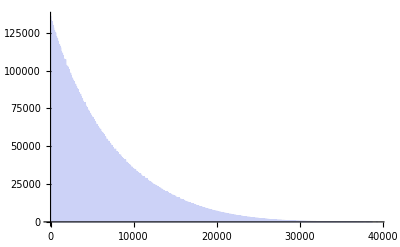

```mathematica
Histogram[lll]
```

```mathematica
Tally[lll]
```

```mathematica
Sort[{{}, {{{1028,2572},{7937,543},{2684,2354},{2139,1683},{17794,208},{337,1537},{14199,314},{2805,2147},{3351,1344},{539,1992},{11664,978},{1265,1904},{1302,3052},{4012,1997},{13154,403},{10646,570},{2052,3428},{2793,1915},{9449,506},{19536,293},{2000,3399},{3464,2066},{13109,243},{1045,2016},{73,1588},{2156,2786},{17160,559},{1550,2480},{7664,1233},{3560,2571},{7574,934},{1380,4216},{5984,1982},{3944,2135},«34968»,{33963,1},{39184,1},{33655,1},{35526,1},{34933,1},{33190,1},{34491,1},{32950,1},{34757,1},{34069,1},{33171,1},{37543,1},{33913,1},{35303,1},{34925,1},{33179,1},{36484,1},{31709,1},{34071,1},{33994,1},{30047,1},{34595,1},{36832,1},{32239,1},{35728,1},{36524,1},{35174,1},{34815,1},{33887,1},{33229,1},{35968,1},{35938,1},{32786,1},{34792,1}}}, {}}]
```

{{0,7621},{1,1637},{2,2303},{3,2169},{4,2984},{5,2043},{6,3021},{7,1904},{8,3306},{9,2258},{10,2843},{11,1789},{12,3952},{13,1752},{14,2739},{15,2775},{16,3540},{17,1789},{18,3197},{19,1675},{20,3659},{21,2492},{22,2543},{23,1652},{24,4263},{25,1983},{26,2447},{27,2312},{28,3485},{29,1669},{30,3647},{31,1606},{32,3578},{33,2349},{34,2512},{35,2357},{36,4130},{37,1620},«34960»,{37615,1},{37619,1},{37632,1},{37645,1},{37704,1},{37743,1},{37770,1},{37790,1},{37875,1},{37908,1},{37914,1},{37923,1},{37935,1},{37960,1},{37984,1},{38016,1},{38027,1},{38040,1},{38042,1},{38054,1},{38112,1},{38186,1},{38193,1},{38228,1},{38241,1},{38286,1},{38310,1},{38312,1},{38319,1},{38444,1},{38468,1},{38482,1},{38518,1},{38590,1},{38692,1},{39158,1},{39184,1},{39266,1}}

```mathematica
1637/19000000
```

1637/19000000

```mathematica
16!*1637/19000000
```

```mathematica
4281325880832/2375//N
```

1.80266×10^9

```mathematica
Block[{mat=Partition[Permute[Range[16],RandomPermutation[16]],4]},{Abs[Det[mat]],mat}]
```

{3471,{{13,2,4,14},{9,7,3,10},{12,15,6,5},{11,1,8,16}}}

```mathematica
Monitor[Sort[Table[Block[{mat=Partition[Permute[Range[16],RandomPermutation[16]],4]},{Abs[Det[mat]],mat}],{i,1,1000000}],First[#1]>First[#2]&],i]
```

{{37984,{{2,8,6,16},{4,9,14,5},{15,1,10,11},{12,13,3,7}}},{37469,{{14,1,12,5},{3,10,15,9},{11,13,6,4},{7,8,2,16}}},{37372,{{10,2,15,9},{6,14,13,1},{16,8,3,7},{4,11,5,12}}},{37180,{{12,13,2,9},{3,7,8,16},{11,5,14,6},{1,15,10,4}}},{37098,{{15,8,1,10},{6,4,12,14},{3,16,5,11},{9,7,13,2}}},{36944,{{5,14,1,11},{2,8,16,9},{12,4,6,15},{13,10,7,3}}},{36921,{{3,7,15,6},{13,14,8,1},{4,11,5,16},{12,2,9,10}}},«999987»,{0,{{9,8,13,2},{7,16,4,15},{5,6,14,11},{3,10,1,12}}},{0,{{1,15,4,8},{10,9,12,3},{2,7,11,16},{6,5,14,13}}},{0,{{4,9,2,5},{16,11,6,13},{1,14,8,7},{15,3,10,12}}},{0,{{5,3,2,1},{9,14,7,15},{6,13,4,16},{8,11,12,10}}},{0,{{11,16,13,5},{7,12,8,4},{9,15,6,2},{1,3,14,10}}},{0,{{15,13,11,1},{5,8,2,3},{10,16,4,6},{7,14,12,9}}}}

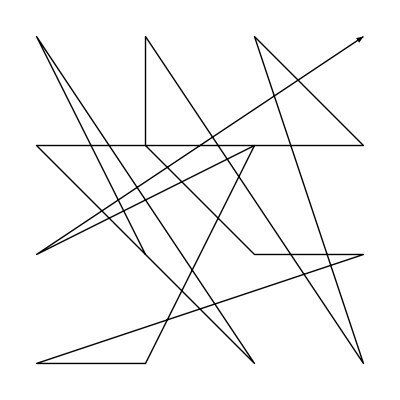
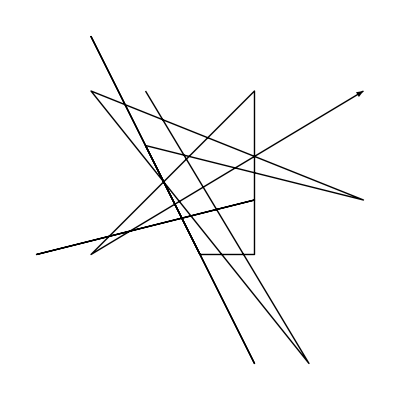
{(2 | 8 | 6 | 16
4 | 9 | 14 | 5
15 | 1 | 10 | 11
12 | 13 | 3 | 7),{-Graphics-,{{-1,2},{2,-3},{-2,2},{3,0},{-1,1},{1,-3},{-2,3},{0,-1},{1,-1},{1,0},{-3,-1},{1,0},{1,2},{-2,-1},{3,2}},-Graphics-}}

```mathematica
GM[{{2,8,6,16},{4,9,14,5},{15,1,10,11},{12,13,3,7}}]
```